# DRS Project | Air flow momentum analysis

```mathematica
vcdf = 50; (*[m/s]*)
```

```mathematica
vreal = 70; (*[m/s]*)
```

```mathematica
Mpaper = {{90,9.75},{80,9.2},{70,8},{60,5.2},{50,0.96},{40,-2.6}};
```

```mathematica
Ms = Mpaper*(vreal/vcdf)^2
```

{{882/5,19.11},{784/5,18.032},{686/5,392/25},{588/5,10.192},{98,1.8816},{392/5,-5.096}}

```mathematica
Mscaled = {{90,19.11},{80,18.032},{70,392/25},{60,10.192},{50,1.8816},{40,-5.096}}
```

{{90,19.11},{80,18.032},{70,392/25},{60,10.192},{50,1.8816},{40,-5.096}}

```mathematica
fit = Fit[Mscaled,{1,x,x^2,x^3},x]
```

-28.6988+0.163214 x+0.0157088 x^2-0.000129396 x^3

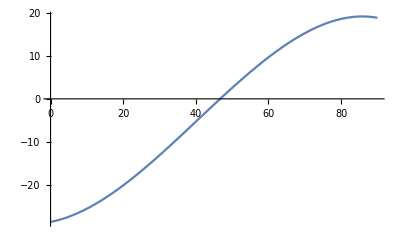

```mathematica
Plot[fit,{x,0,90}]
```